```mathematica
raw={{40,0.337024,0.415294,8.35805*10^-09},{39.5,0.275319,0.370638,4.10482*10^-15},{39,0.213015,0.323943,1.5892*10^-17},{38.5,0.158446,0.27711,1.31149*10^-19},{38,0.117026,0.232789,1.31443*10^-25},{37.5,0.0876637,0.193493,6.68207*10^-32},{37,0.0669683,0.160475,3.47572*10^-38},{36.5,0.0521768,0.133745,1.23544*10^-40},{36,0.0414325,0.112409,1.66066*10^-46},{35.5,0.033477,0.0953612,5.41423*10^-49},{35,0.0274407,0.0816635,4.58135*10^-51},{34.5,0.022734,0.0705391,2.67122*10^-53},{34,0.0189674,0.061407,2.8482*10^-59},{33.5,0.0158892,0.0538148,8.89658*10^-62},{33,0.0133384,0.0474748,7.08075*10^-64},{32.5,0.0112113,0.0421036,5.98116*10^-70},{32,0.00943305,0.0374595,2.4497*10^-76},{31.5,0.00794012,0.0335002,1.04646*10^-82},{31,0.00667057,0.0300689,4.33976*10^-89},{30.5,0.00556495,0.0270787,1.77132*10^-95},{30,0.00456726,0.0244542,7.09647*10^-102},{29.5,0.00362089,0.0221394,2.13387*10^-104},{29,0.00265058,0.0200882,2.70412*10^-110},{28.5,0.00146263,0.0182639,8.88828*10^-117},{28,3.40568*10^-07,0.0166382,3.43046*10^-123},{27.5,5.18763*10^-17,0.015189,9.78433*10^-126},{27,3.26715*10^-17,0.0138995,7.73399*10^-128},{26.5,4.64877*10^-20,0.0127583,5.51861*10^-134},{26,1.2236*10^-20,0.0117422,1.44267*10^-136},{25.5,6.3425*10^-24,0.0108623,1.125*10^-138},{25,1.03228*10^-24,0.0100555,5.58157*10^-141},{24.5,2.79467*10^-28,0.00935696,5.45207*10^-147},{24,3.2394*10^-29,0.00873342,1.47689*10^-153},{23.5,5.44438*10^-33,0.00817831,4.95577*10^-160},{23,6.48272*10^-37,0.00767984,1.25565*10^-162},{22.5,6.36312*10^-41,0.00721461,8.68461*10^-165},{22,5.23362*10^-45,0.00682008,5.56971*10^-171},{21.5,3.65722*10^-49,0.00644549,1.466*10^-177},{21,2.15665*10^-50,0.00610084,3.2452*10^-180},{20.5,1.46284*10^-51,0.0057819,2.46707*10^-186},{20,8.44378*10^-56,0.00548526,5.08634*10^-189},{19.5,3.89433*10^-57,0.00520804,4.11776*10^-191},{19,1.8552*10^-61,0.00494784,1.71954*10^-193},{18.5,7.40104*10^-63,0.00470023,1.71721*10^-199},{18,2.94334*10^-67,0.00447072,3.22446*10^-206},{17.5,7.62139*10^-72,0.0042506,8.13479*10^-209},{17,2.50644*10^-73,0.00404108,5.12944*10^-211},{16.5,7.88956*10^-78,0.00384102,2.27996*10^-213},{16,1.53524*10^-82,0.0036495,1.36528*10^-215},{15.5,4.23488*10^-84,0.00346486,6.4237*10^-218},{15,1.68748*10^-85,0.00328889,3.38707*10^-220},{14.5,3.84208*10^-90,0.00311843,2.14453*10^-226},{14,5.33732*10^-95,0.00295374,3.82742*10^-229},{13.5,1.19041*10^-96,0.00279432,3.55995*10^-231},{13,4.18869*10^-98,0.0026397,1.20086*10^-233},{12.5,1.31117*10^-99,0.00248943,8.60552*10^-236},{12,2.3005*10^-104,0.00234314,3.33521*10^-238},{11.5,2.17611*10^-109,0.00220043,3.01165*10^-244},{11,3.82102*10^-111,0.00206097,4.40896*10^-247},{10.5,1.19062*10^-112,0.00192438,3.63446*10^-249},{10,3.14143*10^-114,0.00179034,6.01892*10^-252}};
```

```mathematica
makeSeries:=Table[Table[{raw[[j]][[1]],raw[[j]][[1+i]]},{j,1,Length[raw]}],{i,1,3}]
```

```mathematica
table[pairs_]:=Grid[Transpose[pairs],Spacings->{3,0}];
```

```mathematica
fm2[name_String,size_,opacity_]:=ResourceFunction["PolygonMarker"][name,Offset@size,{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[opacity]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],0.75]}];
```

```mathematica
markers={fm2["Square",0.4*20,1.0],fm2["Diamond",0.4*17,1.0],fm2["ThreePointedStar",0.4*11,1.0]};
```

```mathematica
ν=0.35
```

0.35

```mathematica
Romero[w_]:=18.2(1-ν)Sqrt[1+ν]+14.5 w
```

```mathematica
Romero[0.9]
```

26.7952

```mathematica
makePlot[romero_]:=Show[ListPlot[makeSeries,PlotMarkers->markers,Joined->True,PlotRange->{-.002,0.1},Frame->True,ImageSize->Large,FrameTicksStyle->Directive[20],PlotLegends->Placed[PointLegend[ConstantArray["",3],LabelStyle->20,LegendLayout->table,LegendMargins->{{0,0},{-30,0}},LegendMarkerSize->{80,50}],Above]],Graphics[{Black,Thick,Dotted,InfiniteLine[{romero,0},{0,1}]}]]
```

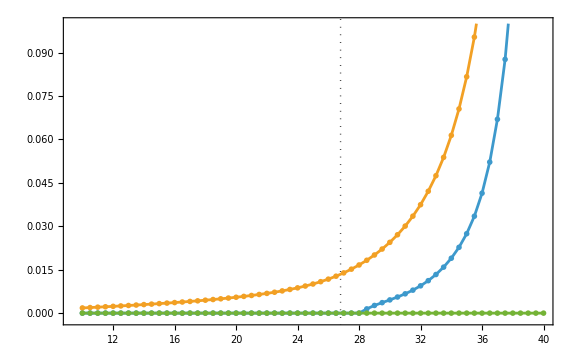

```mathematica
plt = makePlot[Romero[0.9]]
```

```mathematica
Export[NotebookDirectory[]<>"W-0.9.pdf",plt]
```

C:\Users\evoug\Documents\Projects\lateralbuckling\plots\W-0.9.pdf